# q q̄→μ μ in EW theory (SMQCD )

Semplificazione per usare kira. Prodotti scalari sono sostituiti con propagatori, se mancanti-> propagatori ausiliari.
In caso ci siano solo propagatori massimi (WW,ZZ) le masse dei leptoni finali sono poste MM=0
SOstituzioni dei momenti con regole si conservazione:
topology T :K2->P1+P2-K1
U:K1->P1+P2-K2

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SMQCD",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
```

## SMQCD: Feynman rules and Diagrams

## Rules

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3}
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3}
MASSES={MU->0,MU2->0,(*MM->0,MM2->0,*)MD->0,MD2->0,S+T+U->2 MM2}(*MM≠0 nei casi con propagatori gammagamma, gammaZ per togliere divergenze collineari*)
MASSES0={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}(*MM≠0 nei casi con propagatori gammagamma, gammaZ per togliere divergenze collineari*)
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QLl→-1,QUl→2/3,QDl→-1/3}

{QLr→-1,QUr→2/3,QDr→-1/3}

{MU→0,MU2→0,MD→0,MD2→0,S+T+U→2 MM2}

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SMQCD",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SMQCD.mod

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 49 particles (incl. antiparticles) in 18 classes

> $CounterTerms are ON

> 93 vertices

> 121 counterterms of order 1

> 6 counterterms of order 2

classes model {SMQCD} initialized

## Feynman Diagrams

Function tracecolour selects diagrams where colour conservation in present (if output=0 diagram is not considered)

```mathematica
tracecolour[diag_]:=Module[{sunt,trsunt,sumover,g,tab},
diagram=Table[Part[diag,{i}][[1,3]],{i,1,Length[diag]}];
(*trace closed fermion loop*)
tr=Table[Cases[diagram[[i]],_MatrixTrace,Infinity],{i,1,Length[diagram]}];
(*fermionchain without tr*)
input2=Table[DeleteCases[diagram[[i]],_MatrixTrace,Infinity]//.MASSES,{i,1,Length[diagram]}];
sumover=Table[Cases[input2,_SumOver,Infinity],{i,1,Length[input2]}];


Table[If[MemberQ[tr[[i]],SUNT[g_,col_,col_],Infinity]&&MemberQ[sumover[[i]],SumOver[col_,_]], g[i]=0,g[i]=1],{i,1,Length[tr]}];
tab=Table[g[i],{i,1,Length[diagram]}];
tab
];
```

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[2, 2 -> 2, SelfEnergiesOnly];
ins2 = DiagramSelect[InsertFields[tops2, process],Count[LoopFields[##],V[5,_]]===1&];
ins22=DiagramSelect[ins2,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 211 Particles insertions

> Top. 2: 133 Particles insertions

> Top. 3: 133 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 871 Particles insertions

> Top. 11: 1349 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 52 Particles insertions

> Top. 17: 58 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 34 Particles insertions

> Top. 23: 390 Particles insertions

> Top. 24: 342 Particles insertions

> Top. 25: 125 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 3121 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 34 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

Restoring 18 field point(s)

in total: 6853 Particles insertions

```mathematica
selfff=CreateFeynAmp[ins22];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 24 Particles amplitudes

> Top. 2: 48 Particles amplitudes

in total: 72 Particles amplitudes

Sequence[]

> Top. 1 aebe/cfdf/egfh1g1h212g2h.m, 0 diagrams

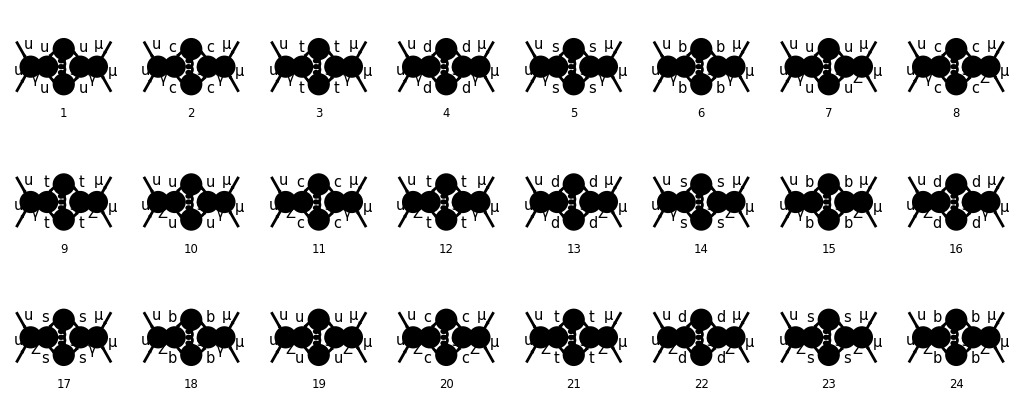

> Top. 1 aebe/cfdf/egfhgh1g21212h.m, 0 diagrams

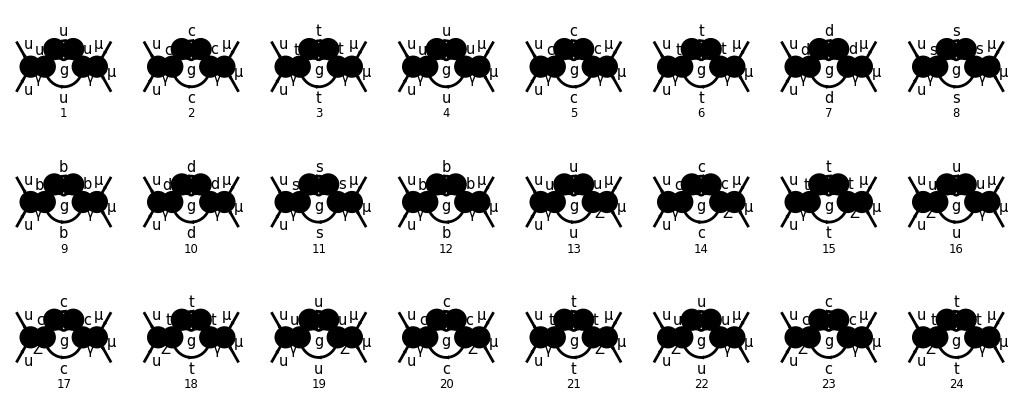

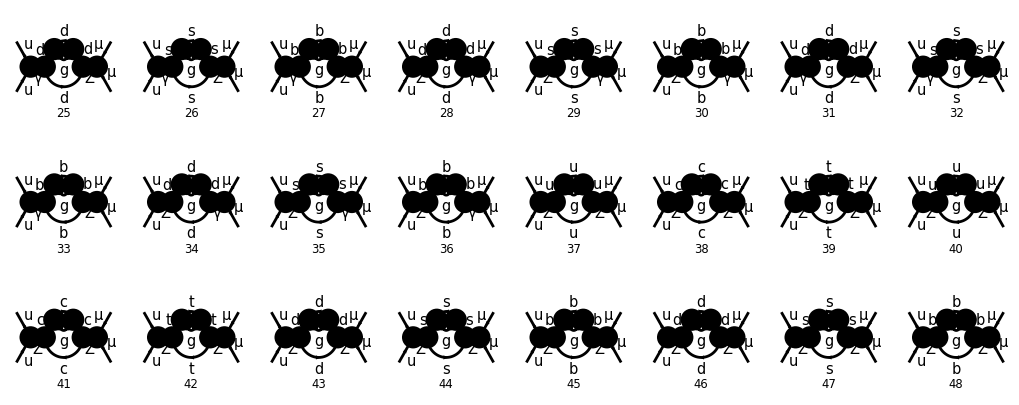

```mathematica
Position[tracecolour[selfff],0]//.List->Sequence(*0 diagrams deleted*)
Table[Paint[ins22[[i]],ColumnsXRows->{8,3},Numbering->Simple,
SheetHeader->None,ImageSize->{1020,406}],{i,1,Length[ins22]}];
```

## Vertices

```mathematica
tops4 = CreateTopologies[2, 2 -> 2, TrianglesOnly];
ins4 =DiagramSelect[InsertFields[tops4, process],Count[LoopFields[##],V[5,_]]===1&];
ins44=DiagramSelect[ins4,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 12 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 34 Particles insertions

> Top. 20: 444 Particles insertions

> Top. 21: 34 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 68 Particles insertions

> Top. 35: 531 Particles insertions

> Top. 36: 68 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 39 Particles insertions

> Top. 40: 0 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

> Top. 43: 0 Particles insertions

> Top. 44: 0 Particles insertions

> Top. 45: 0 Particles insertions

> Top. 46: 0 Particles insertions

> Top. 47: 0 Particles insertions

> Top. 48: 0 Particles insertions

> Top. 49: 0 Particles insertions

> Top. 50: 0 Particles insertions

> Top. 51: 0 Particles insertions

> Top. 52: 0 Particles insertions

> Top. 53: 0 Particles insertions

> Top. 54: 0 Particles insertions

> Top. 55: 0 Particles insertions

> Top. 56: 0 Particles insertions

> Top. 57: 0 Particles insertions

> Top. 58: 0 Particles insertions

> Top. 59: 0 Particles insertions

> Top. 60: 0 Particles insertions

> Top. 61: 0 Particles insertions

> Top. 62: 0 Particles insertions

> Top. 63: 0 Particles insertions

> Top. 64: 0 Particles insertions

> Top. 65: 0 Particles insertions

> Top. 66: 0 Particles insertions

> Top. 67: 0 Particles insertions

> Top. 68: 0 Particles insertions

> Top. 69: 0 Particles insertions

> Top. 70: 0 Particles insertions

> Top. 71: 0 Particles insertions

> Top. 72: 0 Particles insertions

> Top. 73: 0 Particles insertions

> Top. 74: 0 Particles insertions

> Top. 75: 0 Particles insertions

> Top. 76: 0 Particles insertions

> Top. 77: 0 Particles insertions

> Top. 78: 0 Particles insertions

> Top. 79: 0 Particles insertions

> Top. 80: 0 Particles insertions

> Top. 81: 0 Particles insertions

> Top. 82: 0 Particles insertions

> Top. 83: 0 Particles insertions

> Top. 84: 0 Particles insertions

> Top. 85: 0 Particles insertions

> Top. 86: 0 Particles insertions

> Top. 87: 0 Particles insertions

> Top. 88: 0 Particles insertions

> Top. 89: 0 Particles insertions

> Top. 90: 0 Particles insertions

> Top. 91: 0 Particles insertions

> Top. 92: 0 Particles insertions

> Top. 93: 0 Particles insertions

> Top. 94: 12 Particles insertions

> Top. 95: 12 Particles insertions

> Top. 96: 20 Particles insertions

> Top. 97: 26 Particles insertions

> Top. 98: 0 Particles insertions

> Top. 99: 0 Particles insertions

> Top. 100: 24 Particles insertions

> Top. 101: 24 Particles insertions

> Top. 102: 0 Particles insertions

> Top. 103: 0 Particles insertions

> Top. 104: 0 Particles insertions

> Top. 105: 0 Particles insertions

> Top. 106: 0 Particles insertions

> Top. 107: 0 Particles insertions

> Top. 108: 0 Particles insertions

> Top. 109: 0 Particles insertions

> Top. 110: 0 Particles insertions

> Top. 111: 0 Particles insertions

> Top. 112: 0 Particles insertions

> Top. 113: 0 Particles insertions

> Top. 114: 0 Particles insertions

> Top. 115: 0 Particles insertions

> Top. 116: 0 Particles insertions

> Top. 117: 0 Particles insertions

> Top. 118: 0 Particles insertions

> Top. 119: 0 Particles insertions

> Top. 120: 0 Particles insertions

> Top. 121: 0 Particles insertions

> Top. 122: 0 Particles insertions

> Top. 123: 0 Particles insertions

> Top. 124: 0 Particles insertions

> Top. 125: 0 Particles insertions

> Top. 126: 0 Particles insertions

> Top. 127: 0 Particles insertions

> Top. 128: 0 Particles insertions

> Top. 129: 0 Particles insertions

> Top. 130: 0 Particles insertions

> Top. 131: 0 Particles insertions

> Top. 132: 0 Particles insertions

> Top. 133: 0 Particles insertions

> Top. 134: 0 Particles insertions

> Top. 135: 0 Particles insertions

> Top. 136: 0 Particles insertions

> Top. 137: 0 Particles insertions

> Top. 138: 0 Particles insertions

> Top. 139: 0 Particles insertions

> Top. 140: 0 Particles insertions

> Top. 141: 0 Particles insertions

> Top. 142: 0 Particles insertions

> Top. 143: 0 Particles insertions

> Top. 144: 0 Particles insertions

> Top. 145: 0 Particles insertions

> Top. 146: 0 Particles insertions

> Top. 147: 0 Particles insertions

> Top. 148: 0 Particles insertions

> Top. 149: 0 Particles insertions

> Top. 150: 0 Particles insertions

> Top. 151: 0 Particles insertions

> Top. 152: 12 Particles insertions

> Top. 153: 12 Particles insertions

> Top. 154: 20 Particles insertions

> Top. 155: 34 Particles insertions

> Top. 156: 0 Particles insertions

> Top. 157: 0 Particles insertions

> Top. 158: 24 Particles insertions

> Top. 159: 24 Particles insertions

> Top. 160: 0 Particles insertions

> Top. 161: 0 Particles insertions

> Top. 162: 0 Particles insertions

> Top. 163: 0 Particles insertions

> Top. 164: 0 Particles insertions

> Top. 165: 0 Particles insertions

> Top. 166: 0 Particles insertions

> Top. 167: 0 Particles insertions

> Top. 168: 0 Particles insertions

> Top. 169: 0 Particles insertions

> Top. 170: 0 Particles insertions

> Top. 171: 0 Particles insertions

> Top. 172: 0 Particles insertions

> Top. 173: 0 Particles insertions

> Top. 174: 0 Particles insertions

> Top. 175: 0 Particles insertions

> Top. 176: 0 Particles insertions

> Top. 177: 0 Particles insertions

> Top. 178: 0 Particles insertions

> Top. 179: 0 Particles insertions

> Top. 180: 0 Particles insertions

> Top. 181: 0 Particles insertions

> Top. 182: 0 Particles insertions

> Top. 183: 0 Particles insertions

> Top. 184: 0 Particles insertions

> Top. 185: 0 Particles insertions

> Top. 186: 0 Particles insertions

> Top. 187: 0 Particles insertions

> Top. 188: 0 Particles insertions

> Top. 189: 0 Particles insertions

> Top. 190: 0 Particles insertions

> Top. 191: 0 Particles insertions

> Top. 192: 0 Particles insertions

> Top. 193: 0 Particles insertions

> Top. 194: 0 Particles insertions

> Top. 195: 0 Particles insertions

> Top. 196: 0 Particles insertions

> Top. 197: 0 Particles insertions

> Top. 198: 0 Particles insertions

> Top. 199: 0 Particles insertions

> Top. 200: 0 Particles insertions

> Top. 201: 0 Particles insertions

> Top. 202: 0 Particles insertions

> Top. 203: 0 Particles insertions

> Top. 204: 0 Particles insertions

> Top. 205: 0 Particles insertions

> Top. 206: 0 Particles insertions

> Top. 207: 0 Particles insertions

> Top. 208: 0 Particles insertions

> Top. 209: 0 Particles insertions

> Top. 210: 0 Particles insertions

> Top. 211: 0 Particles insertions

> Top. 212: 0 Particles insertions

> Top. 213: 0 Particles insertions

> Top. 214: 0 Particles insertions

> Top. 215: 0 Particles insertions

> Top. 216: 0 Particles insertions

> Top. 217: 0 Particles insertions

> Top. 218: 0 Particles insertions

> Top. 219: 0 Particles insertions

> Top. 220: 28 Particles insertions

> Top. 221: 82 Particles insertions

> Top. 222: 82 Particles insertions

> Top. 223: 151 Particles insertions

> Top. 224: 0 Particles insertions

> Top. 225: 0 Particles insertions

> Top. 226: 0 Particles insertions

> Top. 227: 0 Particles insertions

> Top. 228: 0 Particles insertions

> Top. 229: 0 Particles insertions

> Top. 230: 0 Particles insertions

> Top. 231: 0 Particles insertions

> Top. 232: 0 Particles insertions

> Top. 233: 0 Particles insertions

> Top. 234: 0 Particles insertions

> Top. 235: 0 Particles insertions

> Top. 236: 0 Particles insertions

> Top. 237: 0 Particles insertions

> Top. 238: 0 Particles insertions

> Top. 239: 0 Particles insertions

> Top. 240: 48 Particles insertions

> Top. 241: 101 Particles insertions

> Top. 242: 101 Particles insertions

> Top. 243: 236 Particles insertions

> Top. 244: 0 Particles insertions

> Top. 245: 0 Particles insertions

> Top. 246: 0 Particles insertions

> Top. 247: 0 Particles insertions

> Top. 248: 0 Particles insertions

> Top. 249: 0 Particles insertions

> Top. 250: 0 Particles insertions

> Top. 251: 0 Particles insertions

> Top. 252: 0 Particles insertions

> Top. 253: 0 Particles insertions

> Top. 254: 0 Particles insertions

> Top. 255: 0 Particles insertions

> Top. 256: 0 Particles insertions

> Top. 257: 0 Particles insertions

> Top. 258: 0 Particles insertions

> Top. 259: 0 Particles insertions

> Top. 260: 0 Particles insertions

> Top. 261: 0 Particles insertions

> Top. 262: 0 Particles insertions

> Top. 263: 0 Particles insertions

> Top. 264: 0 Particles insertions

> Top. 265: 0 Particles insertions

> Top. 266: 0 Particles insertions

> Top. 267: 0 Particles insertions

> Top. 268: 0 Particles insertions

> Top. 269: 0 Particles insertions

> Top. 270: 0 Particles insertions

> Top. 271: 0 Particles insertions

> Top. 272: 0 Particles insertions

> Top. 273: 0 Particles insertions

> Top. 274: 0 Particles insertions

> Top. 275: 0 Particles insertions

> Top. 276: 0 Particles insertions

> Top. 277: 0 Particles insertions

> Top. 278: 0 Particles insertions

> Top. 279: 0 Particles insertions

> Top. 280: 0 Particles insertions

> Top. 281: 0 Particles insertions

> Top. 282: 0 Particles insertions

> Top. 283: 0 Particles insertions

> Top. 284: 0 Particles insertions

> Top. 285: 0 Particles insertions

> Top. 286: 0 Particles insertions

> Top. 287: 0 Particles insertions

> Top. 288: 0 Particles insertions

Restoring 18 field point(s)

in total: 2313 Particles insertions

```mathematica
(*Table[Paint[ins44[[i]],ColumnsXRows->{8,1},Numbering->Simple,FieldNumbers->True,
SheetHeader->None,ImageSize->{1012,156}],{i,1,Length[ins4]}];*)
verttt=CreateFeynAmp[ins4];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

> Top. 2: 110 Particles amplitudes

> Top. 3: 14 Particles amplitudes

> Top. 4: 7 Particles amplitudes

> Top. 5: 12 Particles amplitudes

> Top. 6: 13 Particles amplitudes

> Top. 7: 13 Particles amplitudes

> Top. 8: 50 Particles amplitudes

in total: 233 Particles amplitudes

> Top. 1 HFlip[aebe/cfdg/eh1f1g212f2hgh.m], 0 diagrams

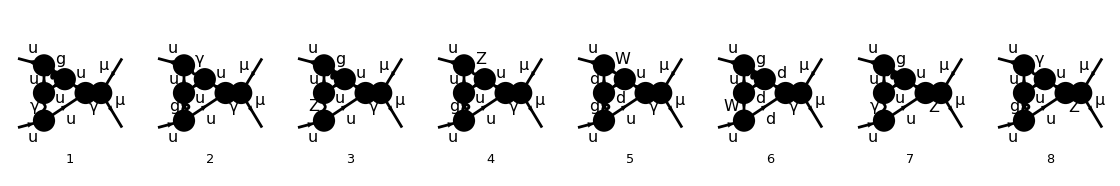

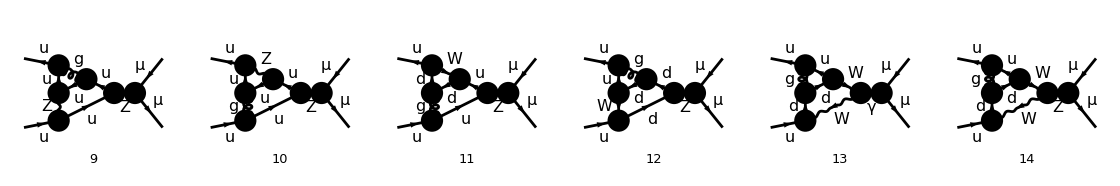

> Top. 1 HFlip[aebe/cfdg/ehfg1f1h212g2h.m], 0 diagrams

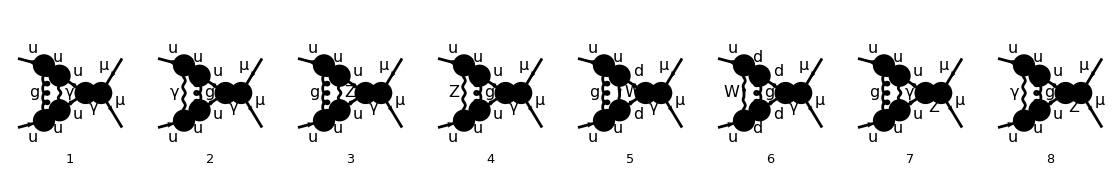

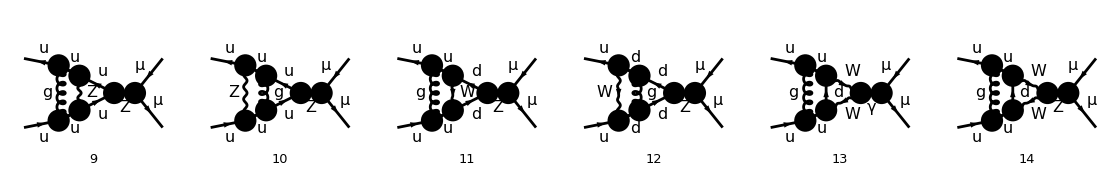

> Top. 1 VFlip[HFlip[aebe/cfdg/eh1f1g212f2hgh.m]], 0 diagrams

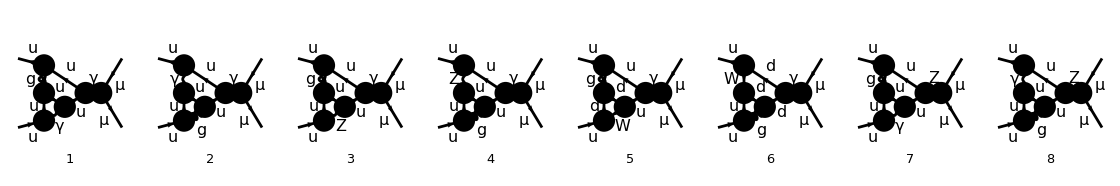

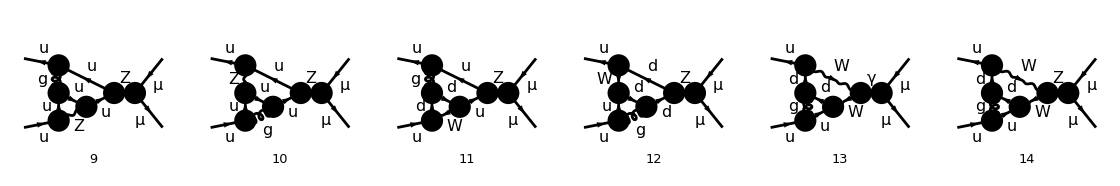

> Top. 1 aebf/cgdh/212g2h1e1fefgh.m, 0 diagrams

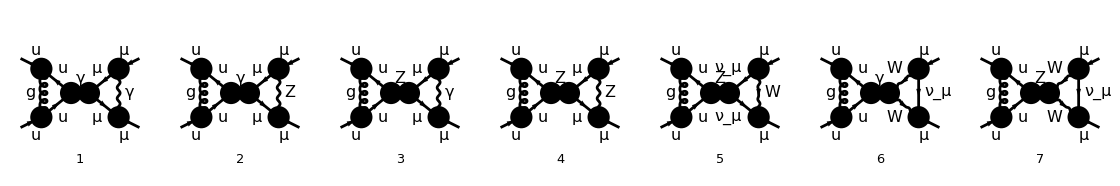

> Top. 1 aebf/cgdg/gh1e1f1h2e2f2h.m, 0 diagrams

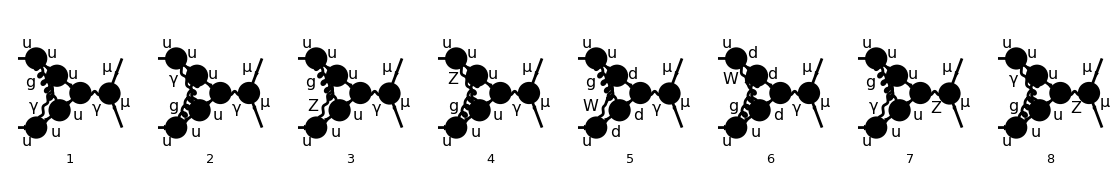

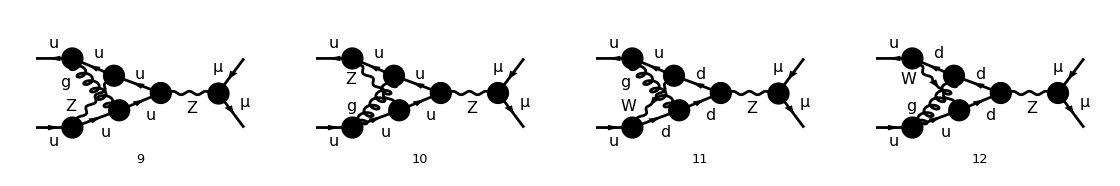

> Top. 1 aebf/cgdg/ghef1e21212hfh.m, 0 diagrams

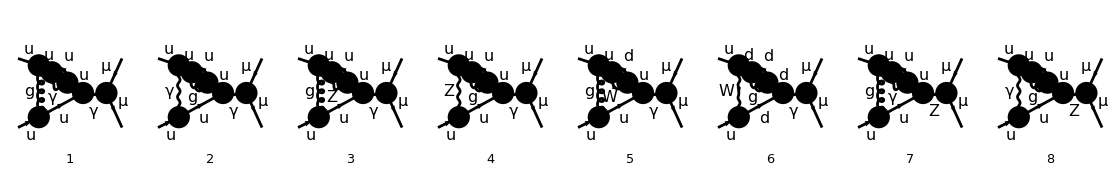

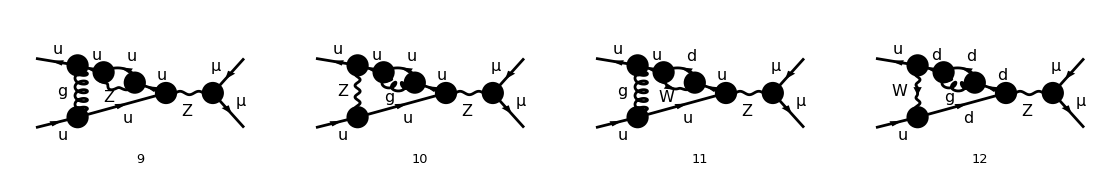

> Top. 1 VFlip[aebf/cgdg/ghef1e21212hfh.m], 0 diagrams

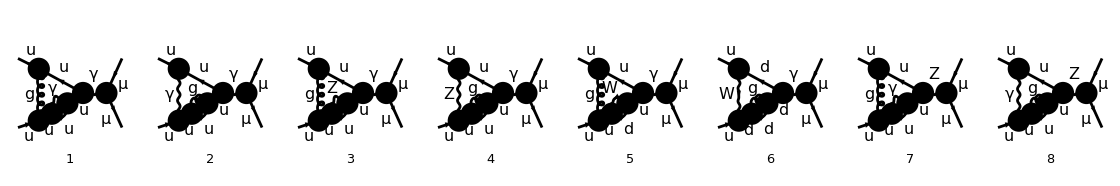

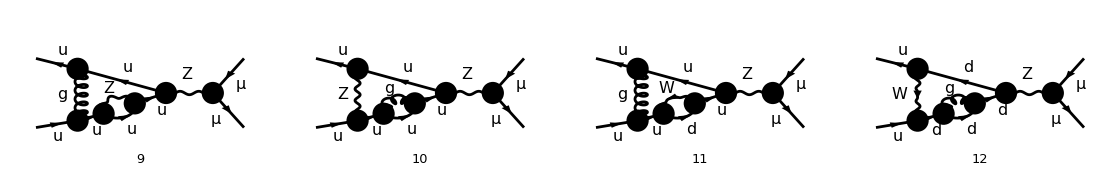

> Top. 1 aebf/cgdg/gheh1e21212ffh.m, 0 diagrams

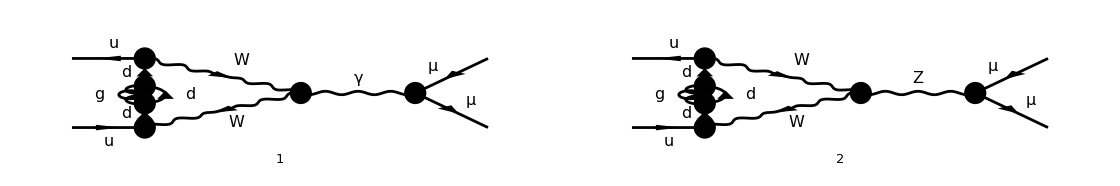

creating amplitudes at level(s) {Particles}

> Top. 1: 14 Particles amplitudes

> Top. 2: 14 Particles amplitudes

> Top. 3: 14 Particles amplitudes

> Top. 4: 7 Particles amplitudes

> Top. 5: 12 Particles amplitudes

> Top. 6: 12 Particles amplitudes

> Top. 7: 12 Particles amplitudes

> Top. 8: 2 Particles amplitudes

in total: 87 Particles amplitudes

```mathematica
pvt=Position[tracecolour[verttt],0]//.List->Sequence;
vert2=DiagramDelete[ins44,pvt];(*diagrams without colour conservation are deleted*)
Table[Paint[vert2[[i]],ColumnsXRows->{8,1},Numbering->Simple,
SheetHeader->None,ImageSize->{1120,186}],{i,1,Length[vert2]}];
verttt=CreateFeynAmp[vert2];
```

## Boxes

```mathematica
tops5 = CreateTopologies[2, 2 -> 2, BoxesOnly]; 
ins5 =DiagramSelect[InsertFields[tops5, process],Count[LoopFields[##],V[5,_]]===1&];
ins55=DiagramSelect[ins5,Count[#,Field[_]->V[5,_]]===1&];(*diagrams with one gluon*)
```

```mathematica
(*Table[Paint[ins55[[i]],Numbering->Simple,
SheetHeader ->None,ColumnsXRows->{5,1},ImageSize->{812,256}],{i,1,Length[ins5]}];*)
box1=CreateFeynAmp[ins5];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 4 Particles amplitudes

> Top. 4: 5 Particles amplitudes

> Top. 5: 4 Particles amplitudes

> Top. 6: 5 Particles amplitudes

> Top. 7: 24 Particles amplitudes

> Top. 8: 24 Particles amplitudes

> Top. 9: 24 Particles amplitudes

> Top. 10: 24 Particles amplitudes

> Top. 11: 4 Particles amplitudes

> Top. 12: 5 Particles amplitudes

in total: 132 Particles amplitudes

> Top. 1 aebf/cgdh/1e1g212e2ffhgh.m, 0 diagrams

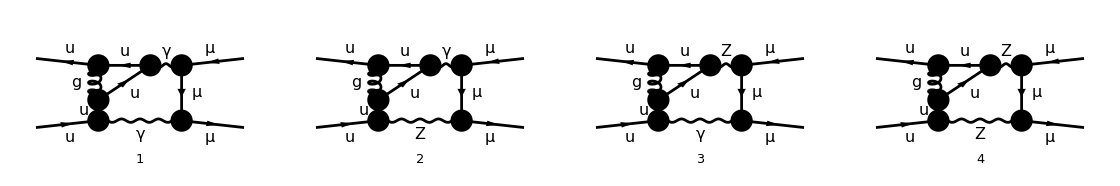

> Top. 1 aebf/cgdh/1e1h212e2ffggh.m, 0 diagrams

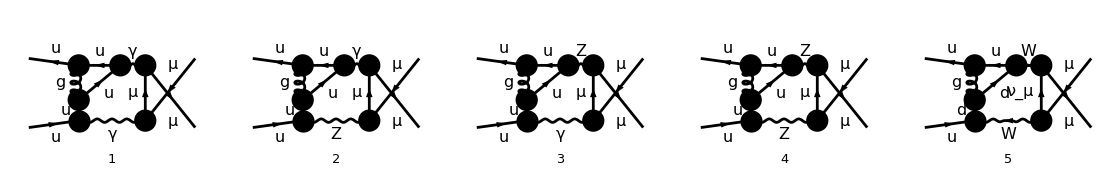

> Top. 1 aebf/cgdh/ef1e1g212f2hgh.m, 0 diagrams

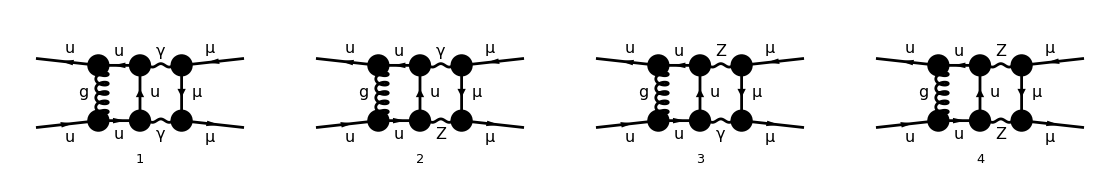

> Top. 1 aebf/cgdh/ef1e1h212f2ggh.m, 0 diagrams

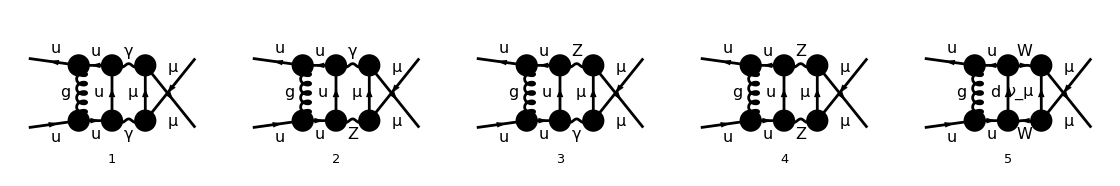

> Top. 1 VFlip[aebf/cgdh/1e1g212e2ffhgh.m], 0 diagrams

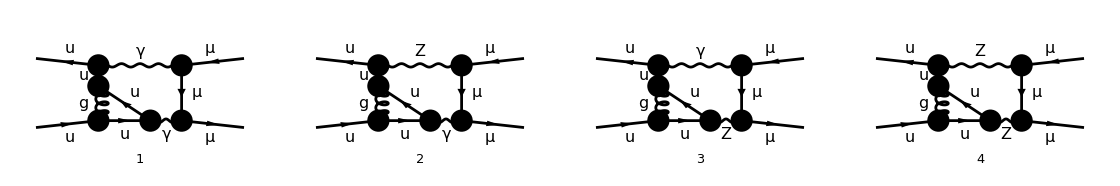

> Top. 1 VFlip[aebf/cgdh/1e1h212e2ffggh.m], 0 diagrams

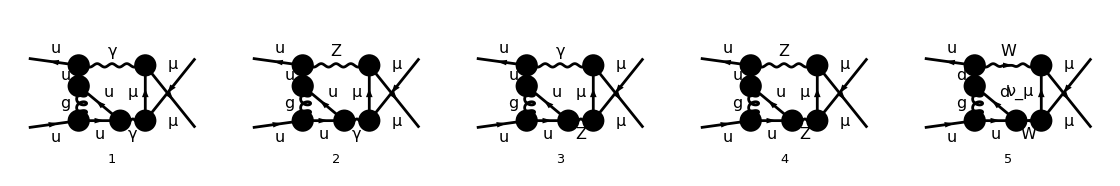

> Top. 1 aebf/cgdh/eg1e21212ffhgh.m, 0 diagrams

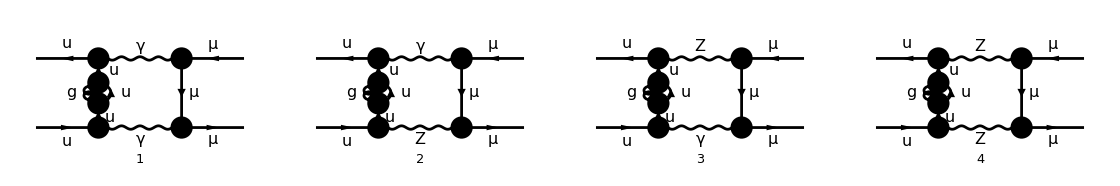

> Top. 1 aebf/cgdh/eh1e21212ffggh.m, 0 diagrams

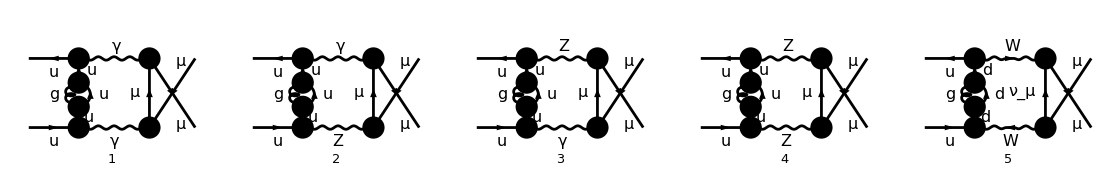

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 4 Particles amplitudes

> Top. 4: 5 Particles amplitudes

> Top. 5: 4 Particles amplitudes

> Top. 6: 5 Particles amplitudes

> Top. 7: 4 Particles amplitudes

> Top. 8: 5 Particles amplitudes

in total: 36 Particles amplitudes

```mathematica
pbx=Position[tracecolour[box1],0]//.List->Sequence;
box2=DiagramDelete[ins55,pbx];(*diagrams without colour conserv. are deleted*)
Table[Paint[box2[[i]],ColumnsXRows->{8,1},Numbering->Simple,
SheetHeader->None,ImageSize->{1120,186}],{i,1,Length[box2]}];
box1=CreateFeynAmp[box2];
```

## Diagrams simplification (box couples)

#### classification

```mathematica
(*set variabili semplificate*)
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
Q2=FourMomentum[Internal,2];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

```mathematica
boxx1=Table[{Union[Cases[Part[box1,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],i},
{i,1,Length[box1]}];
boxx2=Sort[boxx1//.{PropagatorDenominator[Plus[Q1,Times[-1,K1]],MM]->tdenQ1,PropagatorDenominator[Plus[Q1,Times[-1,K2]],MM]->udenQ1,
PropagatorDenominator[Plus[Q2,Times[-1,K1]],MM]->tdenQ2,PropagatorDenominator[Plus[Q2,Times[-1,K2]],MM]->udenQ2}];
boxx3=Gather[DeleteCases[boxx2,tdenQ1|udenQ1|tdenQ2|udenQ2,Infinity],First[#1]==First[#2]&];
bbox=Sort[Table[Cases[boxx3[[i]],_Integer,{2}],{i,1,Length[boxx3]}]]
```

{{9},{18},{27},{36},{1,5},{2,6},{3,7},{4,8},{10,14},{11,15},{12,16},{13,17},{19,23},{20,24},{21,25},{22,26},{28,32},{29,33},{30,34},{31,35}}

```mathematica
totbbox=Table[{Part[box1,{bbox[[i]][[1]]}][[1,3]],Part[box1,{bbox[[i]][[2]]}][[1,3]]},{i,5,Length[bbox]}];
totbboxw=Table[Part[box1,{bbox[[i]][[1]]}][[1,3]],{i,1,4}];
```

```mathematica
(*per divergenze collineari, nei casi con propagatori ZZ o WW si può mettere MM=0, se ho photons NO*)
```

```mathematica
Table[Count[boxx1[[i]],PropagatorDenominator[__,MZ|MW],Infinity],{i,1,Length[boxx1]}]
Table[If[Table[Count[boxx1[[i]],PropagatorDenominator[__,MZ],Infinity],{i,1,Length[boxx1]}][[j]]===2,totbbox[[j]]=totbbox[[j]]*flagMM0//.MASSES0],{j,1,Length[totbbox]}];
```

{0,1,1,2,0,1,1,2,2,0,1,1,2,0,1,1,2,2,0,1,1,2,0,1,1,2,2,0,1,1,2,0,1,1,2,2}

```mathematica
(*esempio*)
tboxzz=totbbox[[12,1]];(*from [[1,1]] to [[16,1]]*)
uboxzz=totbbox[[12,2]];
wwbox=totbboxw[[3]];(*from1 to 4*)
```

mettere 1 per fotone e 2 per z e tboxzz loop diagram

```mathematica
(*BORN*)
born=Part[born1,{2}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES;
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
colourborn=Union[Cases[born,(*_SumOver|*)_IndexDelta,Infinity]]
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times/.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
(*bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)*)
```

{CONJ[v̄[p2,0].(-(ⅈ EL (I3U-QZUl SW2) ga[Lorbn1].om_-)/(CW SW)+(ⅈ EL QZUr SW ga[Lorbn1].om_+)/CW).u[p1,0]],CONJ[ū[k1,MM].(-(ⅈ EL (I3L-QZLl SW2) ga[Lorbn2].om_-)/(CW SW)+(ⅈ EL QZLr SW ga[Lorbn2].om_+)/CW).v[k2,MM]]}

{IndexDelta[Col1,Col2]}

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

#### Loop diagrams propagators

```mathematica
tpropag=DeleteCases[tboxzz//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP//.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
upropag=DeleteCases[uboxzz//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP//.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
wpropag=DeleteCases[wwbox//.MASSES, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP//.PropagatorDenominator[a_,b_,c___]->1/(a^2-b^2)^c
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-MZ2+(q1)^2) (q2)^2 (p2+q2)^2 (-MM2+(q1-k1)^2) (-MZ2+(q1-k1-k2)^2) (p2+q1-k1-k2)^2 (p2+q1+q2-k1-k2)^2)

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-MZ2+(q1)^2) (q2)^2 (p2+q2)^2 (-MM2+(q1-k2)^2) (-MZ2+(q1-k1-k2)^2) (p2+q1-k1-k2)^2 (p2+q1+q2-k1-k2)^2)

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-MW2+(q1)^2) (q2)^2 (p2+q2)^2 (-MW2+(q1-k1-k2)^2) (q1-k2)^2 (p2+q1-k1-k2)^2 (p2+q1+q2-k1-k2)^2)

```mathematica
tpropag=tpropag//.K2->P1+P2-K1
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-(p1)+q1)^2 (-MZ2+(q1)^2) (-MZ2+(-(p1)-p2+q1)^2) (q2)^2 (p2+q2)^2 (-(p1)+q1+q2)^2 (-MM2+(q1-k1)^2))

```mathematica
upropag=upropag//.K1->P1+P2-K2
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-(p1)+q1)^2 (-MZ2+(q1)^2) (-MZ2+(-(p1)-p2+q1)^2) (q2)^2 (p2+q2)^2 (-(p1)+q1+q2)^2 (-MM2+(q1-k2)^2))

```mathematica
wpropag=wpropag//.K1->P1+P2-K2
```

-(SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lor5,Lor6])/(256 π^8 (-(p1)+q1)^2 (-MW2+(q1)^2) (-MW2+(-(p1)-p2+q1)^2) (q2)^2 (p2+q2)^2 (-(p1)+q1+q2)^2 (q1-k2)^2)

#### Colour trace

```mathematica
(*LOOP DIAGRAM COLOUR*)(*self energies sunt in tr loop fermion*)
tabcolor[diag_]:=Module[{t},
diagram=diag;
tbcolour=Table[tb=Part[diagram,{i}][[1,3]];
(*trace closed fermion loop*)
tr=Cases[tb,_MatrixTrace,Infinity];
(*fermionchain without tr*)
input2=DeleteCases[tb,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[trsunt,sunt,colourborn],{i,1,Length[diagram]}];

tbcolour=Union[tbcolour//.{SUNT[g1_,c2_,c5_],SUNT[g2_,c5_,c2_],x__}->{TRc[SUNT[g1],SUNT[g2]],x}//.{SUNT[g1_,c1_,c5_],SUNT[g2_,c5_,c2_],IndexDelta[c1_,c2_]}->TRc[SUNT[g1],SUNT[g2]]];

tbcolour
];
```

```mathematica
tabcolor[box1]
```

{TRc[SUNT[Glu5],SUNT[Glu5]]}

```mathematica
tabcolor[selfff]
```

{{TRc[SUNT[Glu5],SUNT[Glu5]],IndexDelta[Col1,Col2],IndexDelta[Col1,Col2]}}

SUNT[a,k,l] SUNT[b,i,j] IndexDelta[j,k] IndexDelta[a,b]=CF IndexDelta[i,l]
Tr(T a T a ) = C(r)dim(G).

#### Trace functions

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] = -4 I myEps[a1,a2,a3,a4];
myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=MM2;
SP/:SP[K1,K1]:=MM2;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2-MM2;
SP/: SP[P1,K1]:=(MM2-T)/2;
SP/: SP[P2,K2]:=(MM2-T)/2; 
SP/:SP[P1,K2]:=(MM2-U)/2; SP/:SP[P2,K1]:=(MM2-U)/2;
SP/:SP[Q1,Q1]:=Q1^2;
SP/:SP[Q2,Q2]:=Q2^2;
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;

(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM|-MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
move2[a___,1,b___]:=move2[a,b];
move2[a___,1]:=move2[a];
move2[a___,-G5]:=-move2[a,G5];
move2[a___,DiracSlash[-FourMomentum[p__]],b___]:=-move2[a,DiracSlash[FourMomentum[p]],b];
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{tr0f,tr1i,tr2i,tr3i,tr1f,tr2f,tr3f},

(*trace:*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];


(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr2i=Map[Distribute,1/2 DeleteCases[tr1i*chi,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]//.List->Plus//Simplify;(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=tr2i//.move2->TR//.TR->myTr/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr0f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr0f[[i]]]},{i,1,Length[tr0f]}],Plus->Sequence,{2},Heads->True]//.traceff4->move2;
tr2f=Flatten[Map[Distribute,1/2 DeleteCases[tr1f*chf,0,2]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]]//.List->Plus//Simplify;
tr3f=Collect[Collect[tr2f,move2[__],Simplify]//.move2->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand]//.TR->myTr;

Print["stato f ",1/2 DeleteCases[tr1f,0,2]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr3i,tr3f}]

];
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->MM2,SP[K1,K1]->MM2,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->S/2, SP[K1,K2]->S/2-MM2, SP[P1,K1]->(MM2-T)/2, SP[P2,K2]->(MM2-T)/2, SP[P1,K2]->(MM2-U)/2, SP[P2,K1]->(MM2-U)/2};
```

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
(*trd2[x___,DiracSlash[s_],DiracMatrix[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracMatrix[t],y];
trd2[x___,DiracSlash[s_],DiracSlash[t_],DiracSlash[s_],y___]:=2*SP[t,s]*trd2[x,DiracSlash[s],y]-trd2[x,DiracSlash[s],DiracSlash[s],DiracSlash[t],y];*)

TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=MM2*TR[x,y];
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=MM2*TR[x,y];
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
       
TR[a_,b_]= 4 SP[a,b];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_,propag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[-P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[-K1,_],Infinity]&],1];
If[MemberQ[propag,flagMM0,Infinity],tborn3f=tborn3f//.MM->0];(*se propagatori senza photons -> MM=0*)
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[-P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1]//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1]//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

### amplitudes

```mathematica
boxtt=traces[fermiontrace[tboxzz,tpropag][[1]],fermiontrace[tboxzz,tpropag][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/2 move2[gs[p1],ga[Lor1],gs[p2+q1-k1-k2],ga[Lor3],gs[p2+q1+q2-k1-k2],ga[Lor5],gs[p2+q2],ga[Lor4],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[p1],ga[Lor1],gs[p2+q1-k1-k2],ga[Lor3],gs[p2+q1+q2-k1-k2],ga[Lor5],gs[p2+q2],ga[Lor4],gs[p2],ga[Lorbn1],1+G5]}

stato f {{1/2 (move2[MM,ga[Lor6],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor6],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor6],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor6],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor6],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor6],MM,ga[Lor2],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor6],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor6],MM,ga[Lor2],gs[k1],ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor6],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor6],MM,ga[Lor2],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor6],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor6],MM,ga[Lor2],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor6],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor6],gs[q1-k1],ga[Lor2],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor6],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor6],gs[q1-k1],ga[Lor2],gs[k1],ga[Lorbn2],1+G5])}}

```mathematica
boxuu=traces[fermiontrace[uboxzz,upropag][[1]],fermiontrace[uboxzz,upropag][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/2 move2[gs[p1],ga[Lor1],gs[p2+q1-k1-k2],ga[Lor3],gs[p2+q1+q2-k1-k2],ga[Lor5],gs[p2+q2],ga[Lor4],gs[p2],ga[Lorbn1],1-G5],1/2 move2[gs[p1],ga[Lor1],gs[p2+q1-k1-k2],ga[Lor3],gs[p2+q1+q2-k1-k2],ga[Lor5],gs[p2+q2],ga[Lor4],gs[p2],ga[Lorbn1],1+G5]}

stato f {{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor6],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor6],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor6],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor6],gs[k1],ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor6],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor6],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],MM,ga[Lor6],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],MM,ga[Lor6],-MM,ga[Lorbn2],1+G5])},{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1+G5])}}

```mathematica
boxww=traces[fermiontrace[wwbox,wpropag][[1]],fermiontrace[wwbox,wpropag][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/2 move2[gs[p1],ga[Lor1],gs[p2+q1-k1-k2],ga[Lor3],gs[p2+q1+q2-k1-k2],ga[Lor5],gs[p2+q2],ga[Lor4],gs[p2],ga[Lorbn1],1-G5]}

stato f {{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1-G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],gs[k1],ga[Lorbn2],1-G5])},{1/2 (move2[MM,ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1+G5]+move2[gs[k2],ga[Lor2],gs[-(q1)+k2],ga[Lor6],-MM,ga[Lorbn2],1+G5])}}

## Regole sostituzione

```mathematica
(*sostituzioni sono le stesse per caso MM=0 e MM≠0 ma poi dopo aver risostituito regole inverse si pone massa=0 se presente flagMM0*)
```

## box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
```

#### myEps

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Tepsi=iep*tpropag*bornpropag//.MASSES0//Expand,Tepsi=iep*tpropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//.MASSES0//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}],Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}]];
```

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Teps=Teps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.MASSES0//Expand,Teps=Teps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand];
```

#### NO myEps

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Tnepsi=inep*tpropag*bornpropag//.MASSES0//Expand,Tnepsi=inep*tpropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Tneps=ParallelSum[Tnepsi[[i]]*fnep[[j]]//.MASSES0//Expand,{i,1,Length[Tnepsi]},{j,1,Length[fnep]}],Tneps=ParallelSum[Tnepsi[[i]]*fnep[[j]]//Expand,{i,1,Length[Tnepsi]},{j,1,Length[fnep]}]];
```

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],Tneps=Tneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.MASSES0//Expand,Tneps=Tneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand];
```

```mathematica
If[MemberQ[tpropag,flagMM0,Infinity],amplT=Teps+Tneps//.MASSES0,amplT=Teps+Tneps];
```

### Sostituzioni:

```mathematica
(*funzione che trasforma propagatori, tre tipologie di diagrammi: t, u, w*)
intdenT[expr_]:=Module[{t,t1,A1},

dennnt=Sort[Table[If[Head[D1[[i]]]===Power,D1[[i,1]]->Sqrt[dn[i]],D1[[i]]->dn[i]],{i,1,Length[D1]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D1]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituzioni sse la head non è SP*)
t=ReplaceAllRestricted[expr,dennnt,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENt@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D1]}],{j,1,Length[t]}],
expon=DENt@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D1]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
(*lista dei propagatori*)
D1=1/List@@Select[tpropag,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.Power[x__,4]->Power[x,2]
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

q1q2D=Sequence@@Select[D1,MemberQ[#,Q1,Infinity]&&MemberQ[#,Q2,Infinity]&]
D1=Append[DeleteCases[D1,q1q2D],q1q2D](*sposto denom con q1 e q2 in fondo*)
n1=Length[D1]
```

{(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,(-(p1)+q1+q2)^2,-MM2+(q1-k1)^2}

Sequence[(-(p1)+q1+q2)^2]

{(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,-MM2+(q1-k1)^2,(-(p1)+q1+q2)^2}

7

```mathematica
(* se un SP non compare nei dominatori si aggiunge propagatore ausiliario ALL'INIZIO così da essere i primi nella sostituzione ed evitare loop infiniti/errori*)
Complement[Union[Cases[Teps|Tneps,SP[__],Infinity]],Union[Cases[pp1,SP[__],Infinity]]]
auxiliary=%//.SP[p_,q_]->(p-q)^2;
D1=Join[auxiliary,D1]
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

Length[D1]===9
(*è possibile che due SP compaiano a denom. solo in un caso e le sostituzioni vanno in loop. 
Si cercano questi casi e si aggiunge un altro propag ausiliario per uno dei prodotti che non si ripetono*)
(*
propno1=DeleteCases[Cases[Select[pp1,Count[#,SP[__],Infinity]>1&],SP[__],Infinity],SP[Q1,Q2]]
propnotab=Table[Count[Select[pp1,Count[#,SP[__],Infinity]===1&],propno1[[l]],Infinity],{l,1,Length[propno1]}]

If[Count[propnotab,0]>1,(*se ho più zeri, ovvero più el che compaiono solo nei propagatori lunghi, elimino quelli che hanno altri momenti che compaiono in propagatori con funzione Commonest *)
	qqcom=Cases[Commonest[propno1],Q1|Q2,Infinity][[1]];
	propno2=DeleteCases[propno1,SP[qqcom,_],Infinity];
	D1=Prepend[D1,propno2[[1]]//.SP[p_,q_]->(p-q)^2],

	propno1=GroupBy[Tally[propno1],Last][1][[All,1]];
	propnotab=Table[Count[Select[pp1,Count[#,SP[__],Infinity]===1&],propno1[[l]],Infinity],{l,1,Length[propno1]}];
	pzero=FirstPosition[propnotab,0][[1]];

	Which[pzero==="NotFound",
		Print["NO altro porpag auxiliary"];
		D1,
		MemberQ[propno1,Q1,Infinity]&& MemberQ[propno1,Q2,Infinity],(*se ci sono entrambi i Q1,Q2 *)
		Print["aggiungo altro porpag auxiliary"];
		D1=Prepend[D1,propno1[[pzero]]//.SP[p_,q_]->(p-q)^2],
		(MemberQ[propno1,Q1,Infinity]&& MemberQ[propno1,Q2,Infinity])===False,
		Print["NO altro porpag auxiliary"];
		D1
	];

];
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

(*N.RO PROPAG. AUSILIARI, INIZIALI*)
Print["N.RO PROPAG. AUSILIARI, INIZIALI"]
nauxiliar=Length[D1]-n1
Print["N.RO PROPAG. TOTALI:", Length[D1]]
D1*)
```

{SP[q2,k1]}

{(q2-k1)^2,(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,-MM2+(q1-k1)^2,(-(p1)+q1+q2)^2}

False

```mathematica
(*If Length[D1]===9 nessun propag da aggiundere

propag3=Select[pp1,Count[#,SP[__],Infinity]>1&]

prop33=Table[
prop3=Cases[propag3[[j]],SP[__],Infinity];
tabvf[j]=Table[prop3[[l]]->MemberQ[Select[pp1,Count[#,SP[__],Infinity]===1&],prop3[[l]],Infinity],{l,1,Length[prop3]}];
vf=Count[tabvf[j],False,Infinity],{j,1,Length[propag3]}]

poss=Position[prop33,Max[prop33]][[1,1]]

propagaux=Select[tabvf[poss],MemberQ[#,False,Infinity]&&FreeQ[#,SP[Q1,Q2],Infinity]&][[1,1]]*)
```

```mathematica
If[Length[D1]===9,
Print["NO altro porpag auxiliary"],
D1=Prepend[D1,SP[P1,Q2]//.SP[p_,q_]->(p-q)^2];
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2}]
```

{(q2)^2-2 SP[p1,q2]→dn[1],MM2+(q2)^2-2 SP[q2,k1]→dn[2],(q1)^2-2 SP[p1,q1]→dn[3],-MZ2+(q1)^2→dn[4],-MZ2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[5],(q2)^2→dn[6],(q2)^2+2 SP[p2,q2]→dn[7],(q1)^2-2 SP[q1,k1]→dn[8],(q1)^2+(q2)^2-2 SP[p1,q1]-2 SP[p1,q2]+2 SP[q1,q2]→dn[9]}

```mathematica
tkira[expp_]:=Module[{t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];(*seleziono SP*)
t=0;(*flag per evitare loop while infinito*)
While[Length[tbprod]>0,(*fino a che ho SP a numerat*)

If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];(*funzione che semplifica prima SP che compaiono solo in un propagatore. 
																		ex. se (p1-p2+q)^2 (p1+q)^2 scelgo SP[p2,q] perchè l'altro si semplifica con propag piu corto *)
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - , come in (p-q)^2*),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];

t++;If[t>100,Print["ERR"]; Break[]];
];
(*se propagatori con q1 e q2 massivi, (q1,q2 unici temrini da sostituire a numeratore)*)
If[MemberQ[D1,x_+Q1^2,Infinity],
	posq=Position[D1,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
If[MemberQ[D1,x_+Q2^2,Infinity],
	posq=Position[D1,x_+Q2^2][[1,1]];
	ppq=pp1[[posq]]/.Q2^2->0;
	ruleq=Q2^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;

If[MemberQ[expres,flagMM0,Infinity],expres=expres//.MASSES0,expres];

result=intdenT[expres];(*applico funzione che sost con DENt*)

If[MemberQ[result,flagMM0,Infinity],result=result//.MASSES0,result];

result]
```

```mathematica
ParallelMap[tkira,amplT];
```

```mathematica
(*amplTkira=Collect[ParallelMap[tkira,amplT],DENt[__],Simplify];*)
```

## box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Uepsi=iepu*upropag*bornpropag//.MASSES0//Expand,Uepsi=iepu*upropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//.MASSES0//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}],Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}]];
```

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Ueps=Ueps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//.MASSES0//Expand,Ueps=Ueps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//Expand];
```

#### NO myEps

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Unepsi=inepu*upropag*bornpropag//.MASSES0//Expand,Unepsi=inepu*upropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Uneps=ParallelSum[Unepsi[[i]]*fnepu[[j]]//.MASSES0//Expand,{i,1,Length[Unepsi]},{j,1,Length[fnepu]}],Uneps=ParallelSum[Unepsi[[i]]*fnepu[[j]]//Expand,{i,1,Length[Unepsi]},{j,1,Length[fnepu]}]];
```

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],Uneps=Uneps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//.MASSES0//Expand,Uneps=Uneps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//Expand];
```

```mathematica
If[MemberQ[upropag,flagMM0,Infinity],amplU=Ueps+Uneps//.MASSES0,amplU=Ueps+Uneps];
```

### SOSTITUZIONI:

```mathematica
intdenU[expr_]:=Module[{t,t1,A2},
dennnu=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnu,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENu@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENu@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
D2=1/List@@Select[upropag,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.Power[x__,4]->Power[x,2](*riduco potenze alla 4 perchè prodotto di due propag. uguali*)
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

q1q2Du=Sequence@@Select[D2,MemberQ[#,Q1,Infinity]&&MemberQ[#,Q2,Infinity]&]
D2=Append[DeleteCases[D2,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)

n1u=Length[D2]
```

{(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,(-(p1)+q1+q2)^2,-MM2+(q1-k2)^2}

Sequence[(-(p1)+q1+q2)^2]

{(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,-MM2+(q1-k2)^2,(-(p1)+q1+q2)^2}

7

```mathematica
(*(* se un SP non compare nei dominatori si aggiunge propagatore ausiliario ALL'INIZIO*)
Complement[Union[Cases[Ueps|Uneps,SP[__],Infinity]],Union[Cases[pp1u,SP[__],Infinity]]]
auxiliaryu=%//.SP[p_,q_]->(p-q)^2;
D2=Join[auxiliaryu,D2]
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

(*è possibile che due SP compaiano a denom. solo in un caso e le sostituzioni vanno in loop. Si cercano questi casi e si aggiunge un altro propag ausiliario per uno dei prodotti che non si ripetono*)
propno1u=DeleteCases[Cases[Select[pp1u,Count[#,SP[__],Infinity]>1&],SP[__],Infinity],SP[Q1,Q2]]
propnotabu=Table[Count[Select[pp1u,Count[#,SP[__],Infinity]===1&],propno1u[[l]],Infinity],{l,1,Length[propno1u]}]

If[Count[propnotabu,0]>1,(*se ho più zeri, ovvero più el che compaiono solo nei propagatori lunghi, elimino quelli che hanno altri momenti che compaiono in propagatori con funzione Commonest *)
	qqcomu=Cases[Commonest[propno1u],Q1|Q2,Infinity][[1]];
	propno2u=DeleteCases[propno1u,SP[qqcomu,_],Infinity];
	D2=Prepend[D2,propno2u[[1]]//.SP[p_,q_]->(p-q)^2],


	propno1u=GroupBy[Tally[propno1u],Last][1][[All,1]];
	propnotabu=Table[Count[Select[pp1u,Count[#,SP[__],Infinity]===1&],propno1u[[l]],Infinity],{l,1,Length[propno1u]}];
	pzerou=FirstPosition[propnotabu,0][[1]];
	Which[pzerou==="NotFound",
		Print["NO altro porpag auxiliary"];
		D2,
		MemberQ[propno1u,Q1,Infinity]&& MemberQ[propno1u,Q2,Infinity],
		Print["aggiungo altro porpag auxiliary"];
		D2=Prepend[D2,propno1u[[pzerou]]//.SP[p_,q_]->(p-q)^2],
		(MemberQ[propno1u,Q1,Infinity]&& MemberQ[propno1u,Q2,Infinity])===False,
		Print["NO altro porpag auxiliary"];
		D2];

];
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

(*N.RO PROPAG. AUSILIARI, INIZIALI*)
Print["N.RO PROPAG. AUSILIARI, INIZIALI"]
nauxiliaru=Length[D2]-n1u
Print["N.RO PROPAG. TOTALI:", Length[D2]]
D2*)
```

```mathematica
(* se un SP non compare nei dominatori si aggiunge propagatore ausiliario ALL'INIZIO*)
Complement[Union[Cases[Ueps|Uneps,SP[__],Infinity]],Union[Cases[pp1u,SP[__],Infinity]]]
auxiliaryu=%//.SP[p_,q_]->(p-q)^2;
D2=Join[auxiliaryu,D2]
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};
Length[D2]
```

{SP[q2,k2]}

{(q2-k2)^2,(-(p1)+q1)^2,-MZ2+(q1)^2,-MZ2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,-MM2+(q1-k2)^2,(-(p1)+q1+q2)^2}

8

```mathematica
If[Length[D2]===9,
Print["NO altro porpag auxiliary"],
D2=Prepend[D2,SP[P1,Q2]//.SP[p_,q_]->(p-q)^2];
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2}]
```

{(q2)^2-2 SP[p1,q2]→dn[1],MM2+(q2)^2-2 SP[q2,k2]→dn[2],(q1)^2-2 SP[p1,q1]→dn[3],-MZ2+(q1)^2→dn[4],-MZ2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[5],(q2)^2→dn[6],(q2)^2+2 SP[p2,q2]→dn[7],(q1)^2-2 SP[q1,k2]→dn[8],(q1)^2+(q2)^2-2 SP[p1,q1]-2 SP[p1,q2]+2 SP[q1,q2]→dn[9]}

```mathematica
ukira[expp_]:=Module[{t},
expres=expp;
tbprodu=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprodu]>0,
	If[Length[tbprodu]>1,
		tabpu=Table[Count[pp1u,tbprodu[[j]],Infinity],{j,1,Length[tbprodu]}];
		posu=Position[tabpu,Min[tabpu]][[1,1]];
		produ=Cases[expres,SP[__],Infinity][[posu]],
		produ=tbprodu[[1]]];

	(*definita la rule per sostituire SP*)
	For[i=1,i≤Length[pp1u],i++,If[MemberQ[pp1u[[i]],produ,Infinity],Break[]]];
	pp2u=pp1u[[i]]/.produ->0;
	Which[MemberQ[pp1u[[i]],Times[-2,produ],Infinity],
		rul= produ->1/2(Subtract@@pp2u)(*se prod ha segno - *),
		MemberQ[pp1u[[i]],Times[2,produ],Infinity],
		rul=produ->-1/2(Subtract@@pp2u)(*se prod ha segno + *)];
	expres=expres//.rul;
	tbprodu=Union[Cases[expres,SP[__],Infinity]];
	t++;If[t>100,Print["ERR"]; Break[]];
];
(*se propagatori con q1 e q2 massivi, q1,q2 unici temrini da sostituire a numeratore*)
If[MemberQ[D2,x_+Q1^2,Infinity],
	posq=Position[D2,x_+Q1^2][[1,1]];
	ppq=pp1u[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
If[MemberQ[D2,x_+Q2^2,Infinity],
	posq=Position[D2,x_+Q2^2][[1,1]];
	ppq=pp1u[[posq]]/.Q2^2->0;
	ruleq=Q2^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;

If[MemberQ[expres,flagMM0,Infinity],expres=expres//.MASSES0,expres];

result=intdenU[expres];

If[MemberQ[result,flagMM0,Infinity],result=result//.MASSES0,result];

result]
```

```mathematica
ParallelMap[ukira,amplU];
```

```mathematica
(*amplUkira=Collect[ParallelMap[ukira,amplU],DENu[__],Simplify];*)
```

## box W

```mathematica
boxww=boxww//Expand;
```

```mathematica
iepw=Select[boxww[[1]],MemberQ[#,_myEps,Infinity]&];
inepw=Select[boxww[[1]],FreeQ[#,_myEps,Infinity]&];

fepw=Select[boxww[[2]],MemberQ[#,_myEps,Infinity]&];
fnepw=Select[boxww[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Wepsi=iepw*wpropag*bornpropag//.MASSES0//Expand,Wepsi=iepw*wpropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Weps=ParallelSum[Wepsi[[i]]*fepw[[j]]//.MASSES0//Expand,{i,1,Length[Wepsi]},{j,1,Length[fepw]}],Weps=ParallelSum[Wepsi[[i]]*fepw[[j]]//Expand,{i,1,Length[Wepsi]},{j,1,Length[fepw]}]];
```

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Weps=Weps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//.MASSES0//Expand,Weps=Weps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//Expand];
```

#### NO myEps

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Wnepsi=inepw*wpropag*bornpropag//.MASSES0//Expand,Wnepsi=inepw*wpropag*bornpropag//Expand];
```

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Uneps=ParallelSum[Wnepsi[[i]]*fnepw[[j]]//.MASSES0//Expand,{i,1,Length[Wnepsi]},{j,1,Length[fnepw]}],Wneps=ParallelSum[Wnepsi[[i]]*fnepw[[j]]//Expand,{i,1,Length[Wnepsi]},{j,1,Length[fnepw]}]];
```

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],Wneps=Wneps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//.MASSES0//Expand,Wneps=Wneps//.SP[K1,x_]->SP[P1,x]+SP[P2,x]-SP[K2,x]//Expand];
```

```mathematica
If[MemberQ[wpropag,flagMM0,Infinity],amplW=Weps+Wneps//.MASSES0,amplW=Weps+Wneps];
```

### SOSTITUZIONI:

```mathematica
intdenW[expr_]:=Module[{t,t1,A2},

dennnw=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnw,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENw@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENw@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
D2=1/List@@Select[wpropag,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.Power[x__,4]->Power[x,2](*riduco potenze alla 4 perchè prodotto di due propag. uguali*)
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};

q1q2Du=Sequence@@Select[D2,MemberQ[#,Q1,Infinity]&&MemberQ[#,Q2,Infinity]&]
D2=Append[DeleteCases[D2,q1q2Du],q1q2Du](*sposto denom con q1 e q2 in fondo*)

n1u=Length[D2]
```

{(-(p1)+q1)^2,-MW2+(q1)^2,-MW2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,(-(p1)+q1+q2)^2,(q1-k2)^2}

Sequence[(-(p1)+q1+q2)^2]

{(-(p1)+q1)^2,-MW2+(q1)^2,-MW2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,(q1-k2)^2,(-(p1)+q1+q2)^2}

7

```mathematica
(* se un SP non compare nei dominatori si aggiunge propagatore ausiliario ALL'INIZIO*)
Complement[Union[Cases[Ueps|Uneps,SP[__],Infinity]],Union[Cases[pp1u,SP[__],Infinity]]]
auxiliaryu=%//.SP[p_,q_]->(p-q)^2;
D2=Join[auxiliaryu,D2]
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2};
Length[D2]
```

{SP[q2,k2]}

{(q2-k2)^2,(-(p1)+q1)^2,-MW2+(q1)^2,-MW2+(-(p1)-p2+q1)^2,(q2)^2,(p2+q2)^2,(q1-k2)^2,(-(p1)+q1+q2)^2}

8

```mathematica
If[Length[D2]===9,
Print["NO altro porpag auxiliary"],
D2=Prepend[D2,SP[P1,Q2]//.SP[p_,q_]->(p-q)^2];
deninvu=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1u=deninvu//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->MM2,K2^2->MM2}]
```

{(q2)^2-2 SP[p1,q2]→dn[1],MM2+(q2)^2-2 SP[q2,k2]→dn[2],(q1)^2-2 SP[p1,q1]→dn[3],-MW2+(q1)^2→dn[4],-MW2+S+(q1)^2-2 SP[p1,q1]-2 SP[p2,q1]→dn[5],(q2)^2→dn[6],(q2)^2+2 SP[p2,q2]→dn[7],MM2+(q1)^2-2 SP[q1,k2]→dn[8],(q1)^2+(q2)^2-2 SP[p1,q1]-2 SP[p1,q2]+2 SP[q1,q2]→dn[9]}

```mathematica
wkira[expp_]:=Module[{t},
expres=expp;
tbprodu=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprodu]>0,
	If[Length[tbprodu]>1,
		tabpu=Table[Count[pp1u,tbprodu[[j]],Infinity],{j,1,Length[tbprodu]}];
		posu=Position[tabpu,Min[tabpu]][[1,1]];
		produ=Cases[expres,SP[__],Infinity][[posu]],
		produ=tbprodu[[1]]];

	(*definita la rule per sostituire SP*)
	For[i=1,i≤Length[pp1u],i++,If[MemberQ[pp1u[[i]],produ,Infinity],Break[]]];
	pp2u=pp1u[[i]]/.produ->0;
	Which[MemberQ[pp1u[[i]],Times[-2,produ],Infinity],
		rul= produ->1/2(Subtract@@pp2u)(*se prod ha segno - *),
		MemberQ[pp1u[[i]],Times[2,produ],Infinity],
		rul=produ->-1/2(Subtract@@pp2u)(*se prod ha segno + *)];
	expres=expres//.rul;
	tbprodu=Union[Cases[expres,SP[__],Infinity]];
	t++;If[t>100,Print["ERR"]; Break[]];
];
(*se propagatori con q1 e q2 massivi, q1,q2 unici temrini da sostituire a numeratore*)
If[MemberQ[D2,x_+Q1^2,Infinity],
	posq=Position[D2,x_+Q1^2][[1,1]];
	ppq=pp1u[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
If[MemberQ[D2,x_+Q2^2,Infinity],
	posq=Position[D2,x_+Q2^2][[1,1]];
	ppq=pp1u[[posq]]/.Q2^2->0;
	ruleq=Q2^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;

If[MemberQ[expres,flagMM0,Infinity],expres=expres//.MASSES0,expres];

result=intdenW[expres];

If[MemberQ[result,flagMM0,Infinity],result=result//.MASSES0,result];

result]
```

```mathematica
ParallelMap[wkira,amplW];
```

```mathematica
(*amplWkira=Collect[ParallelMap[wkira,amplW],DENw[__],Simplify];*)
```